```mathematica
SetDirectory[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"RABBIT_Packages"}]]
Get["MagicSimulate`"]
Get["PedigreeOrigin`"]
```

D:\Chaozhi\DirectoryWUR\RABBIT Software\RABBIT_Packages

```mathematica
(************************************************************************************************)
```

2

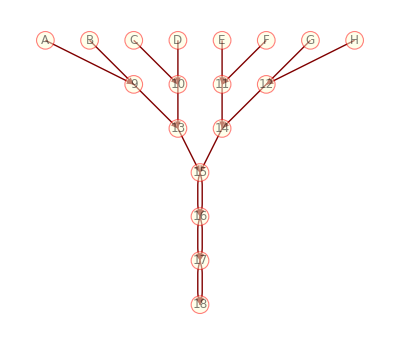

```mathematica
(*1: Pedigree of Native Americans; 
2: RIL by selfing;
3: RIL+ by selfing;
4: RIL by sibling*)
chooseped=RandomChoice[Range[4]]
(*chooseped=2*)
Switch[chooseped,
1,
isautosome=RandomChoice[{True,False}];
ped={{"Generation","MemberID","Gender",{"MotherID","FatherID"}},{0,"A",2,{0,0}},{0,"B",1,{0,0}},{1,"J",2,{0,0}},{1,"L",2,{0,0}},{1,"P",2,{0,0}},{1,"C",1,{0,0}},{1,"M7",1,{"B","A"}},{1,"M8",2,{"B","A"}},{2,"M9",1,{"M7","P"}},{3,"M10",1,{"M9","J"}},{3,"M11",1,{"M9","L"}},{3,"M12",2,{"M7","P"}},{3,"M13",1,{"M7","P"}},{3,"M14",2,{"C","M8"}},{4,"M15",2,{"M10","M12"}},{4,"M16",2,{"M11","M12"}},{4,"M17",1,{"M13","M14"}},{4,"M18",1,{"M13","M14"}},{5,"M19",2,{"M17","M15"}},{5,"M20",1,{"M18","M16"}},{6,"M21",2,{"M20","M19"}},{6,"M22",1,{"M20","M19"}}},
2,
isautosome=True;
nselfing=3;
nFounder=8;
mateScheme=Join[Table["Pairing",{Log[2,nFounder]}],Table["Selfing",{nselfing}]];
ped=simPedigree[setIniPop[nFounder,False],mateScheme],
3,
isautosome=True;
nselfing=3;
mateScheme=Join[{"Pairing","Sibling","CrossPairing","Pairing"},Table["Selfing",{nselfing}]];
nFounder=8;
ped=simPedigree[setIniPop[nFounder,False],mateScheme],
4,
isautosome=RandomChoice[{True,False}];
nsibling=10;
mateScheme=Join[{"Pairing","Pairing"},Table["Sibling",{nsibling}]];
nFounder=8;
ped=simPedigree[setIniPop[nFounder,True],mateScheme];
];
If[chooseped≠1,
nFounder=Count[ped[[All,-1]],{0,0}];
founderid=Take[CharacterRange["A","Z"],nFounder];
ped[[2;;,{2,4}]]=ped[[2;;,{2,4}]]/.Thread[Range[nFounder]->founderid];
(*"Female=1/Male=2/Hermaphrodite=0"*)
ped[[1,3]]="Gender"; 
];
pedigreePlot[ped,ImageSize->400,VertexLabeling->Automatic]
```

```mathematica
(************************************************************************************************)
```

```mathematica
nFounder=Count[ped[[All,-1]],{0,0}]
founderFGL=setfounderFGL[nFounder,True]
indlist=ped[[10;;,2]]
res=pedIdentityPrior[ped,founderFGL,isautosome,indlist];//AbsoluteTiming
res//MatrixForm
```

8

{{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8}}

{9,10,11,12,13,14,15,16,17,18}

{0.0414195,Null}

(Generation | MemberID | Gender | {MotherID,FatherID} | phi(11)_{aa}^mp | R_a^m | R_a^p | rho_{aa}^{mp} | J1112_{aa}^mp | J1121_{aa}^mp | J1122_{aa}^mp | J1211_{aa}^mp | J1213_{aa}^mp | J1222_{aa}^mp | J1232_{aa}^mp
1 | 9 | 0 | {A,B} | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1 | 10 | 0 | {C,D} | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1 | 11 | 0 | {E,F} | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1 | 12 | 0 | {G,H} | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2 | 13 | 0 | {9,10} | 0. | 1. | 1. | 2. | 0. | 0. | 0. | 0. | 1. | 0. | 1.
2 | 14 | 0 | {11,12} | 0. | 1. | 1. | 2. | 0. | 0. | 0. | 0. | 1. | 0. | 1.
3 | 15 | 0 | {13,14} | 0. | 2. | 2. | 4. | 0. | 0. | 0. | 0. | 2. | 0. | 2.
4 | 16 | 0 | {15,15} | 0.5 | 3. | 3. | 5. | 0.5 | 0.5 | 1. | 0.5 | 1. | 0.5 | 1.
5 | 17 | 0 | {16,16} | 0.75 | 3.5 | 3.5 | 5. | 0.5 | 0.5 | 2. | 0.5 | 0.5 | 0.5 | 0.5
6 | 18 | 0 | {17,17} | 0.875 | 3.75 | 3.75 | 4.75 | 0.375 | 0.375 | 2.75 | 0.375 | 0.25 | 0.375 | 0.25)

```mathematica
nFounder=Count[ped[[All,-1]],{0,0}];
founderFGL=setfounderFGL[nFounder,True];
indlist=ped[[{-1,-2},2]];
Print["Calculate for the last pedigree member: ",indlist];
res2=pedAncestryPrior[ped,founderFGL,isautosome,indlist];//AbsoluteTiming
xlab=Transpose[{Range[nFounder],ped[[2;;nFounder+1,2]]}];
Table[MatrixPlot[Normal[res2[[-1,j]]/(10^(-6.)+Max[res2[[-1,j]]])],ImageSize->200,ColorFunctionScaling->False,FrameTicks->{xlab,xlab},Mesh->All,MeshStyle->Directive[GrayLevel[0.7]],PlotLabel->res2[[1,j]]],{j,{7,8,9,10,13}}]
Do[Print[res2[[1,j]],"=", res2[[-1,j]]//MatrixForm],{j,{7,8}}]
```

Calculate for the last pedigree member: {18,17}

{0.326029,Null}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

phi(ij)_{aa}^mp=(0.09375 | 0. | 0. | 0. | 0.0078125 | 0.0078125 | 0.0078125 | 0.0078125
0. | 0.09375 | 0. | 0. | 0.0078125 | 0.0078125 | 0.0078125 | 0.0078125
0. | 0. | 0.09375 | 0. | 0.0078125 | 0.0078125 | 0.0078125 | 0.0078125
0. | 0. | 0. | 0.09375 | 0.0078125 | 0.0078125 | 0.0078125 | 0.0078125
0.0078125 | 0.0078125 | 0.0078125 | 0.0078125 | 0.09375 | 0. | 0. | 0.
0.0078125 | 0.0078125 | 0.0078125 | 0.0078125 | 0. | 0.09375 | 0. | 0.
0.0078125 | 0.0078125 | 0.0078125 | 0.0078125 | 0. | 0. | 0.09375 | 0.
0.0078125 | 0.0078125 | 0.0078125 | 0.0078125 | 0. | 0. | 0. | 0.09375)

R(ij)_a^m=(0. | 0.125 | 0.0625 | 0.0625 | 0.046875 | 0.046875 | 0.046875 | 0.046875
0.125 | 0. | 0.0625 | 0.0625 | 0.046875 | 0.046875 | 0.046875 | 0.046875
0.0625 | 0.0625 | 0. | 0.125 | 0.046875 | 0.046875 | 0.046875 | 0.046875
0.0625 | 0.0625 | 0.125 | 0. | 0.046875 | 0.046875 | 0.046875 | 0.046875
0.046875 | 0.046875 | 0.046875 | 0.046875 | 0. | 0.125 | 0.0625 | 0.0625
0.046875 | 0.046875 | 0.046875 | 0.046875 | 0.125 | 0. | 0.0625 | 0.0625
0.046875 | 0.046875 | 0.046875 | 0.046875 | 0.0625 | 0.0625 | 0. | 0.125
0.046875 | 0.046875 | 0.046875 | 0.046875 | 0.0625 | 0.0625 | 0.125 | 0.)

```mathematica
res3=res2;
Do[res3[[i,5;;]]=Total[Flatten[#]]&/@res2[[i,5;;]],{i,2,Length[res3]}];
res3[[1,5;;]]=StringJoin["sum_",#]&/@res2[[1,5;;]];
Transpose[res3]//MatrixForm
Print["phi(11)_{aa}^mp =",phi11=Total[Diagonal[res2[[-1,7]]]]]
phi11==res[[-2,5]]
res3[[-1,8;;]]==res[[-2,6;;]]
```

(Generation | 6 | 5
MemberID | 18 | 17
Gender | 0 | 0
{MotherID,FatherID} | {17,17} | {16,16}
sum_f(i)_a^m | 1. | 1.
sum_f(i)_a^p | 1. | 1.
sum_phi(ij)_{aa}^mp | 1. | 1.
sum_R(ij)_a^m | 3.75 | 3.5
sum_R(ij)_a^p | 3.75 | 3.5
sum_rho(ij)_{aa}^mp | 4.75 | 5.
sum_Jiiij_{aa}^mp | 0.375 | 0.5
sum_Jiiji_{aa}^mp | 0.375 | 0.5
sum_Jiijj_{aa}^mp | 2.75 | 2.
sum_Jijii_{aa}^mp | 0.375 | 0.5
sum_Jijik_{aa}^mp | 0.25 | 0.5
sum_Jijjj_{aa}^mp | 0.375 | 0.5
sum_Jijkj_{aa}^mp | 0.25 | 0.5)

phi(11)_{aa}^mp =0.75

True

True